# Rapport projekt 31

Murtadha Alobadi, IX1307, mhaao@kth.se

Uppgift 1: Polynomekvation

## Sammanfattning

### Uppgift

Uppgiften gick ut på att man skulle hitta lösningarna till polynomekvationen: x^5+23/3 x^4+25/3 x^3-107/3 x^2-148/3 x+20=0, sedan behövdes en graf ritas för polynomet där nollställena skulle markeras med en röd punkt.

### Resultat

Man fick fram alla x-värdena från polynomekvationen

{-5,-3,-2,1/3,2}

Med dessa värden skulle man rita grafen.

Resultatet blev {{x→-5},{x→-3},{x→-2},{x→1/3},{x→2}}

## Grafen

### Modell för grafen

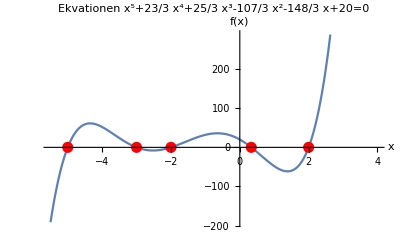

Denna graf visar x-värdena för polynomekvationen x^5+23/3 x^4+25/3 x^3-107/3 x^2-148/3 x+20=0

## Kod

Data för att lösa polynomekvationen:

```mathematica
{x1,x2,x3,x4,x5}=x/.Solve[x^5+23/3 x^4+25/3 x^3-107/3 x^2-148/3 x+20==0,x]
```

Svar på x-värde är :

```mathematica
{-5,-3,-2,1/3,2}
```

Deklarera inne polynomekvationen:

```mathematica
g[x]:=x^5+23/3 x^4+25/3 x^3-107/3 x^2-148/3 x+20
```

För att få x-värde i lista

```mathematica
Solve[g[x]==0,x]
```

X-värde i lista är:

```mathematica
{{x->-5},{x->-3},{x->-2},{x->1/3},{x->2}}
```

Data för att rita polynomekvationen med röda punkter i grafen :

```mathematica
Plot[ƒ[x],{x,-5.5,4},AxesLabel->{"x", "f(x)"},
PlotLabel->"Ekvationen x^5+23/3 x^4+25/3 x^3-107/3 x^2-148/3 x+20=0",Epilog->{PointSize[0.02],Red, 
Point[{{x1, 0},{x2 , 0}, {x3, 0},{x4, 0},{x5,0}}]}]
```

Uppgift 2: Olikhet

## Sammanfattning

### Uppgift

9-En olikhet att lösa
Lös följande olikheter i domänen av alla reella tal:

a)

```mathematica
x+2 >6 x^2
```

b)

```mathematica
(x+1)/((x-2)(2x+3))⩾0
```

c)

```mathematica
(x^2+5)/(x-1)⩽ -1
```

d)

```mathematica
-√(x^2+9)⩾ 2 √x+4
```

e)

```mathematica
√(3x+3)⩾ √x+1
```

10-Sanningsmängder till predikater
Bestäm sanningsmängder till följande predikater i domänen av alla reella tal:

a)

```mathematica
x^3<1 ∧ x^2-x-6  ⩾0
```

b)

```mathematica
(2x-1)(x-3)(2x-5)=0 ∧ √(x^2-x-2)⩾ 2
```

c)

```mathematica
√(x^2-x-2)⩾ √x⋀ x^2-1⩾ 0
```

### Resultat

9)
a)Skriver olikhetern

x+2 >6 x^2

Lös olikheten så att x-värden bestäms.

x-värdena är:

```mathematica
-1/2< x < 2/3
```

Rita en tallinje och markera x-värdet

b) Skriver olikheten

```mathematica
(1+x)/((-2+x) (3+2 x))≥0
```

Löser olikheten så att x-värden bestäms.
x-värdena är:

```mathematica
-3/2<x≤-1||x>2
```

Rita en tallinje och markera x-värdet

c) Skriver olikheten

```mathematica
(-5+x^2)/(-1+x)≤-1
```

Löser olikheten så att x-värden bestäms
x-värdena är:

```mathematica
x≤-3||1<x≤2
```

Rita een tallinje och markera x-värden

d)  Skriver olikheten

```mathematica
-√(x^2+9)⩾ 2 √x+4
```

Löser olikheten så att x-värdet bestäms

De är olösliga. Inget x-värde.

Man markerar inget på tallinjen.

e)  Skriver olikheten

```mathematica
√(3x+3)⩾ √x+1
```

Lös olikheten så att x-värdet bestäms
x-värdet är:

```mathematica
x⩾0
```

Rita en tallinje och markera x-värden och det är alla värden som är större eller lika med 0.

10)
a) Skriver predikatet

```mathematica
x^3<1 ∧ x^2-x-6  ⩾0
```

Lös predikater så x-värdet bestäms 
x-värde är:
x≤-2
Rita en tallinje och markera x-värdet, det är alla värden som är mindre eller lika med -2.

b) Skriver predikatet

```mathematica
(2x-1)(x-3)(2x-5)=0 ∧ √(x^2-x-2)⩾ 2
```

Lös predikatet så x-värdet bestäms 
x-värdet är:
x=3
Rita en tallinje och markera x-värdet,  det är bara talet 3.

c) Skriver predikatet

```mathematica
√(-2-x+x^2)≥√x&&-1+x^2≥0
```

Lös predikatet så x-värdet bestäms.
x-värdena är:
x≥1+√3
Rita en tallinje och markera x-värdet,  x är större eller lika med 1+√3.

## Tallinjen

### Rita tallinjen till Olikhet

9- a) x-värdena är:  -1/2<x<2/3

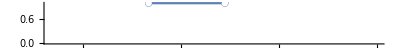

b) x-värdena är: -3/2<x≤-1||x>2

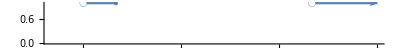

c) x-värdena är: x≤-3||1<x≤2

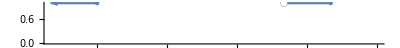

d) Olöslig

-Graphics-

e) x-värdet x≥0

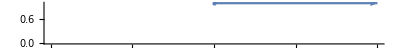

10- a) x-värdet är: x≤-2

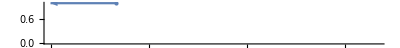

b) x-värdet är: x=3

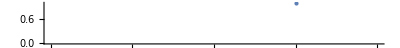

c) x-värdet är: x≥1+√3

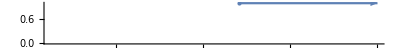

## Kod

9) a)

Deklarera given data

```mathematica
(x+2)>6x^2
```

För att bestäma x-värdet i olikheten.

```mathematica
Reduce[%,x]
-1/2<x<2/3
```

Rita tallinje med hjälp av:

```mathematica
NumberLinePlot[2+x>6 x^2,{x,-2,3}]
```

b)

Deklarera given data

```mathematica
(x+1)/((x-2)(2x+3))⩾0
```

För att bestäma x-värdet i olikhet

```mathematica
Reduce[%,x]
-3/2<x≤-1||x>2
```

Rita tallinje

```mathematica
NumberLinePlot[(1+x)/((-2+x) (3+2 x))≥0,{x,-2,3}]
```

c)

Deklarera given data

```mathematica
(x^2-5)/(x-1)⩽-1
```

För att bestäma x-värden i olikheten

```mathematica
Reduce[%,x]
x≤-3||1<x≤2
```

Rita tallinje

```mathematica
NumberLinePlot[(-5+x^2)/(-1+x)≤-1,{x,-4,3}]
```

d)

Deklarera given data

```mathematica
-√(x^2+9)⩾2 √x+4
```

För att bestäma x-värdet i olikheten

```mathematica
Reduce[%,x]
False
```

Rita tallinje

```mathematica
NumberLinePlot[-√(x^2+9)⩾2 √x+4,{x,-4,3}]
```

e)

Deklarera given data

```mathematica
√(3x+3)⩾ √x+1
```

För att bestäma x-värdet i olikheten

```mathematica
Reduce[%,x]
x≥0
```

Rita tallinje

```mathematica
NumberLinePlot[√(3x+3)⩾ √x+1,{x,-3,3}]
```

10) a)

Deklarera given data

```mathematica
x^3 < 1 ∧ x^2 - x - 6 ⩾ 0
```

För att bestäma x-värdet i olikheten

```mathematica
Reduce [x^3<1 ∧ x^2-x-6⩾0]
x≤-2
```

Rita tallinje

```mathematica
NumberLinePlot[x≤-2, {x, -3,2}]
```

b)

Deklarera given data

```mathematica
(2x−1)(x−3)(2x−5)==0  ∧ √(x^2-x-2) ⩾2
```

För att bestäma x-värdet i olikheten

```mathematica
Reduce[(-3+x) (-5+2 x) (-1+2 x)==0&&√(-2-x+x^2)≥2]
x=3
```

Rita tallinje

```mathematica
NumberLinePlot[x==3, {x, 0,4}]
```

c)

Deklarera given data

```mathematica
√(x^2-x-2)⩾√x ∧x^2-1⩾0
```

För att bestäma x-värdet i olikheten

```mathematica
Reduce[√(-2-x+x^2)≥√x&&-1+x^2≥0]
x≥1+√3
```

Rita tallinje

```mathematica
NumberLinePlot[x≥1+√3, {x, 1,4}]
```

Uppgift 3: Binomisk ekvation

## Sammanfattning

### Uppgift

Finn lösningen till ekvationen z^6=-3+3i och visa grafiskt att dessa ligger på en cirkel i komplexa talplanet.

### Resultat

Man fick alla komplexa värden för z från ekvationen:

```mathematica
z^6=-3 + 3ⅈ
```

Man ritade  en cirkel och märkerade alla z-värden.

Resultatet blev {-1.1755-0.486907 ⅈ,1.1755+0.486907 ⅈ,-0.166075-1.26146 ⅈ,0.166075+1.26146 ⅈ,1.00942-0.774557 ⅈ,-1.00942+0.774557 ⅈ}

## Cirkel

### Modell för grafen

```mathematica
z^6=-3 + 3ⅈ
```

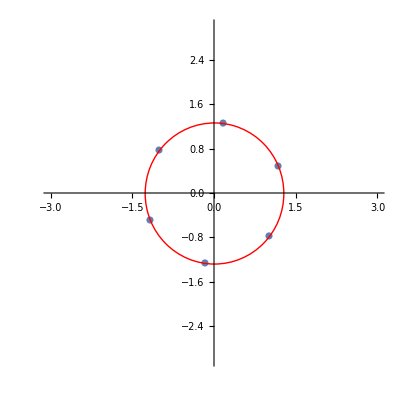

Cirkeln bevisar alla z-värden.

## Kod

Data för att lösa ekvationen:

```mathematica
{x1,x2,x3,x4,x5}=Z=z/.Solve[z^6==-3+3I]//N
```

Svar på z-värde samt att få den som en lista:

{-1.1755-0.486907 ⅈ,1.1755+0.486907 ⅈ,-0.166075-1.26146 ⅈ,0.166075+1.26146 ⅈ,1.00942-0.774557 ⅈ,-1.00942+0.774557 ⅈ}

Data för att rita cirkel med röd färg :

```mathematica
ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@Z,AspectRatio->1,Epilog->{Red,Circle[{0,0},Abs[Z[[1]]]]},
PlotRange-> {{-3,3},{-3,3}}
]
```

Uppgift 4: Logik

## Sammanfattning

### Uppgift

1.Propositioner
Betrakta följande propositioner:
p_1:(√2∈R)∧ ∼(√2∈Q)
p_2:(1/2∈Z)∨ ∼(1/2∈Q)
p_3:∼(-4∈N)→∼(-4∈Z)
p_4:(2.5∈Q) ⟷  2.5∈R

b) Vilka av dessa propositioner är sanna?

### Resultat

Man ska ta reda på vilka av dessa som är sanna

p_1:(√2∈R)∧ ∼(√2∈Q)
p_2:(1/2∈Z)∨ ∼(1/2∈Q)
p_3:∼(-4∈N)→∼(-4∈Z)
p_4:(2.5∈Q) ⟷  2.5∈R

Med hjälp av logik kan man få veta vilka som är sanna

Resultatet blev:
p_1:True
p_2:True
p_3:False
p_4:True

## Kod

Data för att lösa propositioner : 
p_1:

```mathematica
Element[Sqrt[2],Reals]&& NotElement[Sqrt[2],Rationals]
True
```

p_2:

```mathematica
Element[1/2,Integers]||Element[1/2,Rationals]
True
```

p_3:

```mathematica
Not[Element[-4,Integers]&& -4>0]⇒Not[Element[-4, Integers]]
False
```

p_4:

```mathematica
Element[5/2,Rationals]⧦Element[2.5, Reals]
True
```

Uppgift 5: Ekvationslösning och grafer

## Sammanfattning

### Uppgift

En D’Artagnan jagas av Richeliue. Båda rider så snabbt de kan. D’Artagnan rider med en hastighet av 42 km/h och Richeliue med 57 km/h. Richeliue är 60 meter efter D’Artagnan och det är 250 vmeter till stadsporten där D’Artagnan kan komma undan. Bestäm om Richeliue hinner i kapp D’Artagnan och i så fall vilken tidpunkt och sträcka innan stadsporten det sker. Illustrera tidsförloppet grafiskt på lämpligt sätt.

### Resultat

Låt (v1) ge första hastighet och (v2) ge andra hastighet då få en funktion av sträcka (s1) och (s2).

v1=42/3.6 
v2=57/3.6

Den efterfrågade tiden kan beräknas enligt. 
Piecewise[{{, s1[t_]:=60+v1 t

s2[t_]:=v2 t}}]

Resultatet blev {{t→14.4}}

## Grafen

### Modell för grafen

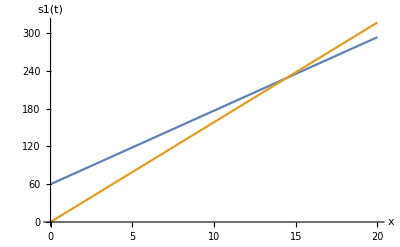

Grafen bevisar linjen för v1 och v2  och var de möts.

## Kod

Deklarera v1 och v2

```mathematica
v1=42/3.6
```

11.6667

```mathematica
v2=57/3.6
```

15.8333

Deklarera funktion av sträcka

```mathematica
s1[t_]:=60+v1 t
s2[t_]:=v2 t
```

För att få svaret i lista med hjälp av

{{t→14.4}}

Att rita grafen

```mathematica
Plot[{s1[t],s2[t]},{t,0,20},AxesLabel->{"x", "s1(t)"}]
```

För att få tiden åt s1 och s2 när de har samma tid

```mathematica
t0=t/.Solve[s1[t]==s2[t],t]
```

{14.4}

För att få s1

```mathematica
s1[t0]
```

{228.}

För att få s2

```mathematica
s2[t0]
```

{228.}

## REFERENSER

Mathematica program, Version Number:12.1.1.0